# Custom Probability Density Function

## How to generate a PDF (distribution) in mathematica

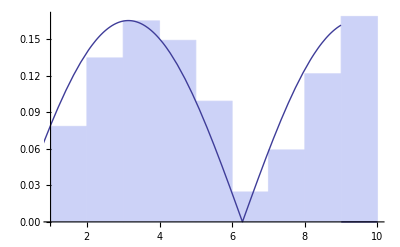

```mathematica
ProbDensity[x_]:=Abs[Sin[x/2]]
ProbDist=ProbabilityDistribution[ProbDensity[x],{x,0,9,1}];
nfactor=Sum[ProbDensity[x],{x,0,9,1}];
Cus=RandomVariate[ProbDist,10000];
Show[
Histogram[Cus,10,"ProbabilityDensity"],
Plot[PDF[ProbDist,x]/nfactor,{x,0,10},PlotStyle->Thick]
]
```

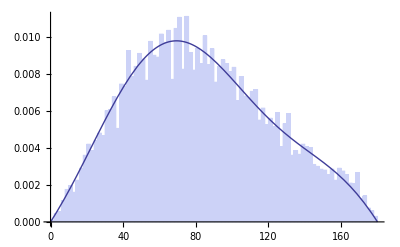

```mathematica
ProbDensity[x_]:=(1+0.3Sin[2x °])Sin[x °]
ProbDist=ProbabilityDistribution[ProbDensity[x],{x,0,180,1}];
nfactor=Sum[ProbDensity[x],{x,0,180,1}];
Cus=RandomVariate[ProbDist,10000];
Show[
Histogram[Cus,100,"ProbabilityDensity"],
Plot[PDF[ProbDist,x]/nfactor,{x,0,180},PlotStyle->Thick]
]
```

```mathematica
SphericalPlot3D[{1,(1+0.3Sin[2θ]Cos[ϕ])},{θ,0,π},{ϕ,-π,π},PlotStyle->{Directive[Opacity[0.5],Red],Directive[Opacity[0.5],Blue]}]
```

-Graphics3D-

```mathematica
Plot3D[ProbDensity2D[x,y],{x,0,180},{y,0,360}]
```

-Graphics3D-

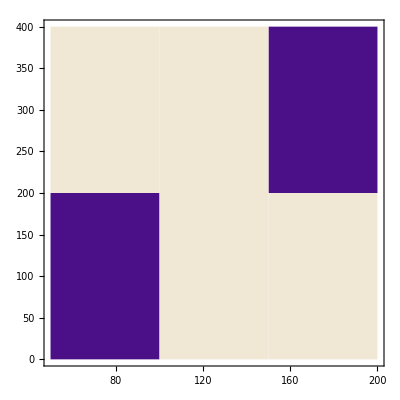

```mathematica
pdfθ=ProbabilityDistribution[Sin[θ °],{θ,0,180,1}];
pdfϕ=ProbabilityDistribution[1,{ϕ,0,360,1}];
Cus=Table[{RandomVariate[pdfθ],RandomVariate[pdfϕ]},{i,1,10}];
DensityHistogram[Cus]
```

```mathematica
n=400;
ϕList=Table[RandomReal[{-π,π}],{i,1,n}];
pdfθ=ProbabilityDistribution[(1+Sin[2 θ °]Cos[ϕ]),{θ,0,180,1},{ϕ,0,1}];
θList=Table[RandomVariate[pdfθ],{i,1,n}];
Histogram[θList]
```

-Graphics-

```mathematica
RandomVariate[pdfθ,{2,2}]
```

RandomVariate::noimp: Sampling from ProbabilityDistribution[1 + Cos[x2]\ Sin[2\ x1\ °], {x1, 0, 180, 1}, {x2, 0, 1}] is not implemented.

RandomVariate[ProbabilityDistribution[1+Cos[x2] Sin[2 x1 °],{x1,0,180,1},{x2,0,1}],{2,2}]

```mathematica
di=ProbabilityDistribution[Beta[3/4,1/2]/(Sqrt[2] Pi^2) 1/(1+x^4+y^4),{x,-Infinity,Infinity},{y,-Infinity,Infinity}];
cus=RandomVariate[di]
```

RandomVariate::noimp: Sampling from ProbabilityDistribution[Gamma[3/4]/√2\ (1 + x1^4 + x2^4)\ π^3/2\ Gamma[5/4], {x1, -∞, ∞}, {x2, -∞, ∞}] is not implemented.

RandomVariate[ProbabilityDistribution[Gamma[3/4]/(√2 (1+x1^4+x2^4) π^(3/2) Gamma[5/4]),{x1,-∞,∞},{x2,-∞,∞}]]